Plots that demonstrate the angle for total internal reflection (from Snell’s law).

```mathematica
ClearAll[thetaT]

thetaT[i_, ni_, nt_] = ArcSin[ Sin[i] ni/nt ] ;
p[ n1_, n2_] := Plot[ thetaT[i, n1, n2], {i, 0, Pi/2}, AxesLabel->{"θ_i", Row[{"θ_t, n_1/n_2 = ", n1/n2}]}, Ticks -> {{0, Pi/8, Pi/4, Pi/2}, {0, Pi/8, Pi/4, Pi/2}} 
] ;

Manipulate[ 
p[n1, n2]
,{{n1, 1, "n_1"}, 1, 10},{{n2, 1, "n_2"}, 1, 10}]
```

r

```mathematica
<<peeters` ;
```

```mathematica
peeters`setGitDir[ "figures\\ece1228-emt" ]
```

C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1228-emt

```mathematica
peeters`exportForLatex["reflectionForN2gtN1Fig1", p1]
peeters`exportForLatex["reflectionForN1gtN2TotalInternalReflectionFig2", p2]
```

{reflectionForN2gtN1Fig1.eps,reflectionForN2gtN1Fig1pn.png}

{reflectionForN1gtN2TotalInternalReflectionFig2.eps,reflectionForN1gtN2TotalInternalReflectionFig2pn.png}

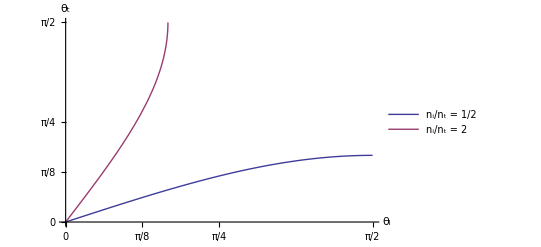

{reflectionForBothFig3.eps,reflectionForBothFig3pn.png}

```mathematica
(*p1 = p[ 1, 2] 
p2 = p[2, 1]*)
p3 = Plot[ {thetaT[i, 1,2],thetaT[i, 2,1]}, {i, 0, Pi/2}, AxesLabel->{"θ_i", "θ_t"}, Ticks -> {{0, Pi/8, Pi/4, Pi/2}, {0, Pi/8, Pi/4, Pi/2}} ,
PlotLegends->Placed[ {"n_i/n_t = 1/2", "n_i/n_t = 2"}, {Right, Top}], PlotRange -> Full 
] 
peeters`exportForLatex["reflectionForBothFig3", p3]
```